# Introduction to Random Walks

[see -> BSSRDF->TheoreticalFoundation->dEon->Zero-Variance Theory for Efficient Subsurface Scattering]
We’ll see in a bit that with absorption, scattering and phase functions we can model the appearance of translucent materials. The unbiased approach to this, is a brute-force random walk. Basically the whole process is to :

- sample a free-path-length distribution (i.e. to move the walk one step) 
- sample a phase function (i.e. changing walk direction) 
- until we escape at boundary where eventually we sample its BRDF

Note here we don’t take into account boundary conditions like Fresnel, that simply means we pretend there’s no interaction between our random walks and the boundary itself if not for sampling the boundary BSDF.. proper interactions would account for example for the walk that could get back into the medium once reached the boundary. 
[Note that however Fresnel may still play a role with the BSSRDF layer as generally the diffuse contribution, to obey energy conservation, is multiplied by 1-Fresnel]

So what are we doing here ? Considering light as a flux of particles (photon beam) that interact with other particles in a medium. This is the photonic interpretation of electromagnetic scattering by macroscopic particles and has its roots in Einstein’s paper on the photoelectric effect (1905).. where photons are considered energy quanta localized at points in space and that behaves as complete units.. and are these phenomenological photons that form the incident beam of light that change direction upon scattering on the macroscopic particles or just disappear due to absorption.

[see -> BSSRDF->TheoreticalFoundation->Gustav Mie and the Fundamental Concept of Electromagnetic Scattering by Particles]
Furthermore in Mie theory (1908), the scattering object is defined as a finite volume with a refractive index different from that of the surrounding infinite homogeneous medium. And so on with the traditional intuitive perception of scattering seen as a plane electromagnetic wave propagating in an infinite non-absorbing medium without a change in its intensity until it will be in the presence of particles, so that the difference between the total field in the presence of the particle and the original field that would exist in the absence of the particle might be thought of as the field scattered by the particle.. in other words, the total field in the presence of the particle is represented as the sum of the respective incident (original) and scattered fields.. thus, it is the modification of the total electromagnetic field caused by the presence of the particle that is called electromagnetic scattering.

Now here, what do we mean with, - phenomenological ? That can be said to be a physical phenomenon. So can we say that electromagnetic scattering is a physical phenomenon ? Of course, - we would say. But. It is not however to be treated as a solitary physical process. So the question that belongs to this could be, - where does it end the physics and starts the mathematics ? 

[see -> BSSRDF->TheoreticalFoundation->dEon->An Hitchhiker’s Guide to Multiple Scattering]
Once physics has been used to derive the distributions that govern the random flight of one particle, the physics ends and the transport theory begins. Once we have completely defined the properties of a scattering problem, we begin the core statistical analysis of considering a point particle with initial position and direction drawn randomly from the source distribution. The particle then undergoes an alternating sequence of straight displacements and scattering events. The distances between scattering events and the deviations in angle at each scattering event are random variables drawn from given distributions. The process is eventually terminated when the particle is randomly absorbed, or when the particle escapes the finite system.

So let’s highlight some strong physical points about scattering and our particles.
We limit our attention here to linear scattering :
- particles do not interact with each other and with other particles in the walk
- particles do not alter the nature of the medium they are scattering/absorbing into

A linear transport problem is defined by :
- specifying a medium/scene, 
- its properties and boundaries,  
- a set of light sources. 
- and a detector sensitivity over the phase space (rendering camera)

What follows belongs to classical ‘analog’ sampling of random walks, for that we employ this estimator :
- a particle arrives at the boundary entering the medium along a cosine direction μi
- initial particle weight is 1
- sample direction with phase fnc
- sample displacement with exponential law
- check if the particle last step did cross the boundary
- if not, calculate its new weight and sample a new dir and step
- if yes sample boundary BSDF

# Material Properties

Absorption, Scattering and Phase functions

[see -> Reflection from Layered Surfaces due to Subsurface Scattering]
The surface of skin, leaves, snow, paint etc. is comprised of one or more layers composed of a mixture of randomly distributed particles or inhomogeneities embedded in a translucent media. Particle distributions can also exist, in which case the material properties are given by the product of each particle’s properties times the number of particles per unit volume.

The intensity of the backscattered and transmitted light depends on the absorption and scattering properties of the material. These cross sections are interpreted as the probability per unit length of an interaction of a particular type. In classical physics, this probability often converges to a deterministic proportion of excitation energy involved in the process, so that, the cross section specifies the amount of optical power scattered from light of a given irradiance.

σ_a= absorption coefficent
σ_s= scattering coefficent
σ_t= σ_a+ σ_s= extinction coefficent

These are physical units so they should be used with a scaling parameter, i.e. for meters use a x1000.

The mean free path is equal to the reciprocal of the total cross section, 1/σ_t.
An important quantity is the albedo, which equals W = σs/σt. If the albedo is close to 1, the scattering cross section is much greater than the absorption cross section, whereas if the albedo is close to 0, absorption is much more likely than scattering. That’s also why the albedo is considered as the scattering efficency factor.

However while there’re measurement of ‘sigmas’ (aka, optical parameters) that will approach specific materials like grapefruit potato skin leaves etc. [see -> A Practical Model for Subsurface Light Transport, fig.5; for Skin, see -> Tissue Optics: Light Scattering Methods and Instruments for Medical Diagnosis; for Leaves, see -> Fukshansky et al., 1993; both mentioned in -> Light Diffusion in Multi-Layered Translucent Materials] it is really cumbersome to rely on those when one wants some artistic control. So we generally remap Albedo and MeanFreePath.. ie. SSS color and SSS radius to the above quatities with the following :

```mathematica
(* see -> Practical and Controllable Subsurface Scattering for Production Path Tracing *)
remapVolToScatter[albedo_,radius_]:=Module[{a=albedo, d=radius},
α=1-ⅇ^(−5.09406*a+2.61188*a^2−4.31805*a^3);
s=1.9−a+3.5(a−0.8)^2;
σ=1.0/(d*s);
x=σ*α;
{σ,x,α} (*--gives back sigmaT, sigmaS and single-scattering Alpha --*)
];
```

```mathematica
rgbAlbedo=List[0.5,0.75,0.3];
rgbRadius = List[1,0.3,0.2];
remapVolToScatter[rgbAlbedo,rgbRadius]
```

{{0.58309,2.87666,2.0202},{0.531952,2.83235,1.52685},{0.912298,0.984595,0.755792}}

Now, let’s analyse what we get back as optical parameters when our albedo is mid grey.. ie. the characterization of sigmas will be mainly from the mfp.

```mathematica
rgbAlbedo=List[0.5,0.5,0.5];
rgbRadius = List[1,0.3,0.2];
remapVolToScatter[rgbAlbedo,rgbRadius]
```

{{0.58309,1.94363,2.91545},{0.531952,1.77317,2.65976},{0.912298,0.912298,0.912298}}

Let’s look at the Red channel for example, it is 1. What we see is that we have higher Greens and Blues than Red which has 1 as mfp. What this means ? That the Greens and Blues will be absorbed/scattered more than Reds. Each component of these coefficients indicates how much Red, Blue and Green is absorbed and scattered by the medium.

So we have two main material properties here: absorption and scattering. These apply to all objects. When an object is black it absorbs almost all the light. If an object is white, it absorbs very little light and scatters most of it back. We may think that only absorption accounts for the darkening of the material but effectively also scattering does .. when a light is scattered not all light will reach our eyes because its directions are deflected to other paths. 

Generally with ‘scattering’ we intend a surface material property, aka surface scattering which is generally modelled by a BRDF. Here instead we will deal with subsurface scattering. However under a general definition this is the same as surface scattering.. it is just that particles substrate at the surface will also absorb light so the ‘surface’ is going deeper into the material and as a result of that it won’t scatter back necessarly from the same point it did hit the material originally. So we can consider a BRDF an approximation (where x_o=x_i) of a full BSSRDF and formalize the BSSRDF definition as the ratio between outgoing radiance at x_o, as a result of incoming differential radiant flux ⅆΦ at x_i.

[see -> A Practical Model for Subsurface Light Transport and Skin Rendering: Reflectance and Integration]
Because we’re interested in the outgoing radiance that will hit back our eyes or camera sensor, given a BSSRDF, the outgoing radiance L_o is computed by integrating the incident radiance L_i over incoming direction and area :

L_o(x_o,OverVector[w_o])=∫_A ∫_(2π) (S(x_i,w⃗)_i;x_o,OverVector[w_o])L_i(x_i,(w⃗)_i)(n⃗.(w⃗)_i)ⅆ w_iⅆA(x_i)

Note the x_i, x_o where for a BRDF x_o= x_i; 
S(·) is the BSSRDF : (ⅆL(x_o,(w⃗)_i))/(ⅆϕ(x_i,(w⃗)_o))
Note from the above L_o(·) , the cosine term n⃗.(w⃗)_i diminishes the density of photons arriving within dA for large angles ..

(d^2 Φ)/(dAd w⃗)=(w⃗·n⃗)L(x,w⃗)

aka, the flux received at xi within a differential area, dA, from a direction within a differential angle around (w⃗)_i

The BSSRDF S relates the differential outgoing radiance at x_o to the differential incident flux at x_i as :

dL_o=(x_o,(w⃗)_o)=S(x_i,(w⃗)_i,x_o,(w⃗)_o)dΦ_i(x_i,(w⃗)_i)

Light propagation in a particinpating medium is described by the radiative transport equation (RTE), 
aka volume rendering linear integro-differential equation (VRE):

(w⃗·OverVector[∇])L(x,w⃗)=-σ_tL(x,w⃗)+σ_s∫_(4π) p(w⃗,OverVector[w'])ⅆ w'

[see -> Skin Rendering: Reflectance and Integration]
The equation describes the rate of change in radiance. 
Where σ_t and σ_s are our extinction and scattering coefficents. The quantity of photons scattered per unit traveled is given by σ_s(x) and the quantity absorbed is given by σ_a(x). The rate of loss in radiance flowing in the direction −ω⃗ at x is accounted for by the first term on the right side of equation. The second term accounts for gain in radiance due to in-scattering. This is done by integrating the radiance over all possible directions. During integration the radiance is scaled by σ_s(x) and the phase function p(x, w⃗',w⃗). The former will give us the portion of radiance from  w⃗' scattered at x and the latter will give us the portion of this contribution which scatters specifically into the direction w⃗.


Where ∫_(4π) p(w⃗,OverVector[w']) is the phase function that obeys ∫_(4π) p(x,w⃗',w⃗)ⅆ w⃗'=1.
That is a function describing the dependence of scattered radiance on scattering angle. The phase function is a dimensionless and normalized version of the scattering function, such that the integral of the phase function over 4π steradians is unity. The phase function for a given wavelength is a property of the medium, not of the incident radiation.

The phase function is the angular distribution of light intensity scattered by a particle at a given wavelength. It is given at an angle θ which is relative to the incident beam. The phase function is the intensity (radiance) at θ relative to the normalized integral of the scattered intensity at all angles. It is defined as :

P(θ)=(F(θ))/(∫_0^π F(θ)sinθⅆθ)

where F is the radiance and P(θ) is the probability of a photon being scattered in a particular direction θ. That also means that when integrated over the sphere it must equal zero, thing known as the ‘normalization condition’ and shown by :

1/(4π)∫_0^(2π) ∫_0^π p(cosθ)sinθⅆθⅆϕ

Note that the azimuthal dependence ϕ of P is often removed, which is possible under the assumption of a spherical particle. Eventually as there’re many BRDFs for surface scattering, there’re many phase functions for subsurface scatter.

Phase fncs share a similarity with BRDFs in that phase functions are reciprocal, where the trivial case regards that cos(-θ)=cos(θ). Phase functions can be isotropic or anisotropic and we’ll see them in detail in the further chapters. Another distinction is that for particles at microscopic level we generally use Raylegh scattering while for those at macroscopic level with use Mie theory (Henyey-Greenstein is a generalization of the latter).

Now getting back to our BSSRDF, the incoming radiance will decrease exponentially with distance s.
This is referred to as the reduced radiance. which is the radiance that has entered the medium but has not yet scattered or been absorbed. And that’s the first part into which the radiance is decomposed (the diffuse radiance L_d(x,w⃗) being the second term).

L_ri(x_i+s(w⃗)_i,(w⃗)_i)=e^-σ_ts L_i(x_i,(w⃗)_i)

for more on the topic of volume rendering, [see -> LightTransport->theory->1993 - (Direct) Volume Rendering]

# Exponential Random Walks

Distance Sampling

Τ=1-ϵ^-σs

This gives back the actual ratio of uncollided particles to initial particles, having travelled s with absorption σ. 
That corresponds to a change in radiance along the ray as light travels through a medium filled with absorbing particles.
Take care that here T(ransmittance) is a CDF, not a PDF.

```mathematica
Clear[σ,s];
transmittance = 1-Exp[-(σ*s)];

𝒟=ProbabilityDistribution[{"CDF",transmittance},{s,0,∞}]
D[transmittance,s](* or do it straightly with differentiation *)
```

ProbabilityDistribution[Piecewise[{{ⅇ^(-x σ) σ, x>0}, {0, True}}],{x,0,∞}]

ⅇ^(-s σ) σ

This is the actual PDF, i.e. the normalization of an exponential distribution.

tPDF=σⅇ^-σs
t=ⅇ^-σs

this is the probability that a particle has an interaction in ds having travelled s into a medium σ. 
This probability is a logarithmic relationship between the transmission of light and the product of the absorption in the medium and the distance travelled.

Now, if we lookup ‘exponential distribution’ in Wikipedia we’ll see it defined as :
“The probability distribution of the time between events in a Poisson point process”.
A Poisson point process is characterized via the Poisson distribution. 
The Poisson distribution is the probability distribution of a random variable K such that the probability that K equals k is:

P(X=k)=(λ^k e^-λ)/(k!)

Now what’s the probability that something will happen between events.. zero (because that something happens.. is the event)

P(X=0)=(λ^0 e^-λ)/(0!)=e^-λ

How are our events ? Indipendent.
And if instead of dealing with the unit time we deal with a period, then

P(X=0)*P(X=0)*P(X=0)*...=e^(-λt)

which is our exponential distribution :)

Now our random walk is considered instantaneous, ain’t taking any time at all, ie. is non-transient, but we can still use the same paradigm when we consider each indipendent particle collision as our event. Because here we’re not interested in the events (which would be the scattering) themself but in the ‘in-between events’ (which is absorption).. but what is in-between each particle collision ?.. the distance (of light travelling in the matter) it will take to reach the next particle (collision event).

So what’s telling us the PDF above as a general case ?.. the density of time until the next event will happen.
Effectively λ (in a Poisson distribution) is not a time duration but a rate of the unit of time, that’s also why in an Exponential distribution, it is 1/λ which is the decay rate instead.

So what’s between our events when not in a ‘time’ framework but in a ‘physical/geometric’ one, matter. 
The primary causes of attenuation in matter are the photoelectric effect and the compton scattering.
How is matter characterized here ? With an extinction coefficent, aka the total cross section.

So we can say that ⅇ^(-s σ) is the statistical density of the material expressed as transmission.
Why do we need it ? Because as we’ll see below by inverting the integral of a density, we’ll get a sample of the quantity that bounds that density, in this case we’ll get a distance sample that characterize our light transmission so that, the sample corresponds (is proportional) to a certain density that needs to be considered if we wanna our sample to be unbiased. 

When we do something like this : ξ=Ft(x) (where F is the above CDF and ξ is a uniform random variate ∼(0,1)), - what are we saying actually ? That the cumulative probability of the radiant flux to reach a distance s without incurring in a collision, is our random number. Or in other words, the probability that a certain distance will be travelled is the differential of the material density (as transmission) around that point or also that a certain distance travelled is proportional to the rate of change of the radiance flux in the material by the cross section (that’s why we wanna sample a distance to simulate stochastically via a randomwalk the material transmittance).

ⅆΦ/ⅆs=(Φ(s+ⅆs)-Φ(s))/ⅆs=-σΦ⇒Φ=e^-σs

[see → https://en.wikipedia.org/wiki/Beer-Lambert_law for the derivation]
[see → https://www.sciencedirect.com/topics/mathematics/exponential-distribution for other insights]
[see → The Exponential Distribution and Its Applications , for a full complete treatment]

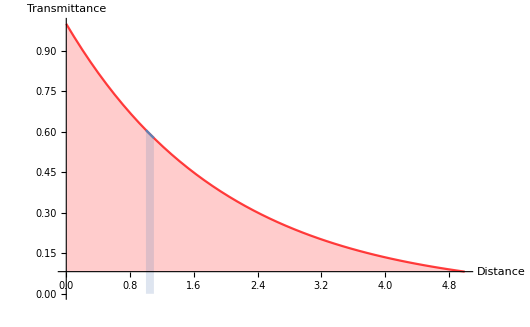

```mathematica
Clear[f,s,σ];
f[s_,σ_ ]:= Exp[-(s*σ)];

With[{σ=0.5},
Show[
Plot[f[s,σ],{s,0,5},PlotRange->All,PlotStyle->{Red, Opacity[0.75]},AxesLabel->{"Distance","Transmittance"},Filling->Axis,LabelStyle->Directive[RGBColor[0.5],Bold]],
Plot[f[s,σ],{s,1,1.1},Filling->0,PlotRange->All]
]]
```

I mean, the flux at (s+ds) minus the flux at s divided by ds is the reduced radiance, ie. the radiance multiplied by the material cross section, so that formally, the difference in radiant flux divided by a infinitesimal displacement s is the radiance around s and that, is (proportional to) the exponential decay that occurs within s - s+ds.

So let's see how to sample exponential distances by inverting the CDF of an exponential distributions.

We saw that the quantity describing the path length between scatterings can be considered a random variable being characterized by some probability density function defined for a defined interval such that :

∫_a^b p(ξ)ⅆξ=1

Now we can simulate a random event for which the variable falls with frequency p(x)dx in the interval (x, x+dx) by choosing a random number R from a uniform distribution ϵ (0,1) and requiring :

R=∫_a^x p(ξ)ⅆξ

We know that integrating the interval from the lower-bound to our variable is effectively computing the CDF of the probability function till that point. All we’re left to do is to solve for the variable of interest. This the Monte Carlo method.

```mathematica
Assuming[{σ>0},Solve[ξ==1-ⅇ^(-(s σ)),s]](* 1-e^(-(sσ))is the CDF of our exponential *)
```

{{s→ConditionalExpression[(2 ⅈ π C[1]+Log[1/(1-ξ)])/σ,C[1]∈ℤ]}}

Where we get our sampling routine as

```mathematica
-Log[1/(1-ξ)]/σ;(* the (1/1-ξ) is still a random number ξ∼U(0,1) so eventually we get *)
sampleDistance=-Log[1-ξ]/σ;
(* while it looks like we save a substraction by using just the ξ.. 
it's better to leave it as 1-ξ because ξ could turn out to be 0 and so we'd take the Log[0] which is undefined while it's not for Log[1] *)
```

We could have used also Mathematica build-ins

```mathematica
Clear[σ,x]
PDF[ExponentialDistribution[σ],x]
CDF[ExponentialDistribution[σ],x]
InverseCDF[ExponentialDistribution[σ],ξ]
```

Piecewise[{{ⅇ^(-x σ) σ, x≥0}, {0, True}}]

Piecewise[{{1-ⅇ^(-x σ), x≥0}, {0, True}}]

ConditionalExpression[Piecewise[{{-Log[1-ξ]/σ, ξ<1}, {∞, True}}],0≤ξ≤1]

sampleExpDis=-Log[1-ξ]/σ

Let’s check this really works ..

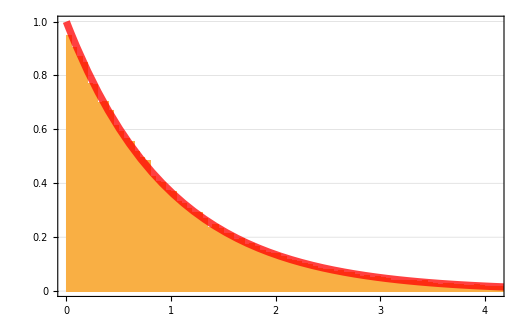

```mathematica
Clear[f,s,σ];
f[s_,σ_ ]:= Exp[-(s*σ)];
sampleExpDis[σ_]:=-Log[1-#]/σ&[RandomReal[]]
With[{σ=1.0},
Show[
Histogram[ParallelTable[sampleExpDis[σ],{i,Range[10^5]}],256,"PDF",PlotTheme->"Business"],
Plot[f[s,σ],{s,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]
]]
```

Let’s plot some stuff ..

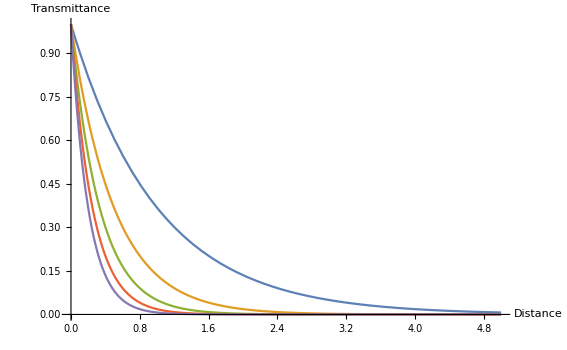

```mathematica
Plot[Table[f[s,σ],{σ,1,5}]//Evaluate,{s,0,5},PlotRange->All,AxesLabel->{"Distance","Transmittance"},LabelStyle->Directive[RGBColor[0.5],Bold]]
(*Plot[Evaluate[Table[f[s,σ],{σ,0,1}]],{s,0,10},PlotRange->All]*)(*same as above*)
```

As we can see the more into the medium the less transmittance.
Also the higher the transmittance the less distance to travel for full absorption.

Analytically draw transmittance over the unit square

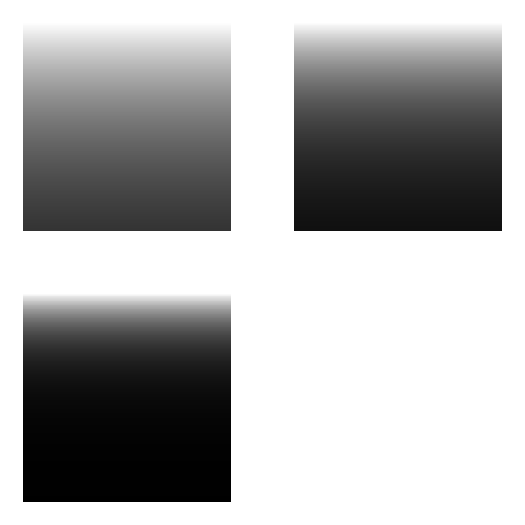

```mathematica
(* here we just need the exponential fnc to feed it with the s-distance over the unit square, we divide the unit by the freq factor to get a smooth gradient and use a matrixplot to draw the gradient *)

ClearAll["Global`*"];
freq=256;
fncScaling=False;
imageSize = Medium;

f[i_,σ_]:=Module[{s,d,vSize},
vSize=20;
s=(i/(freq))*vSize;(* get step distance in 0,1 *)
d=Exp[-(s*σ)];
1-d
]

GraphicsGrid[{
{With[{σ=0.08},
expdata=Table[f[x,σ],{x,freq},{y,freq}];(* yup, we could just eval one single column *)
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
],With[{σ=0.14},
expdata=Table[f[x,σ],{x,freq},{y,freq}];
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
]},
{With[{σ=0.32},
expdata=Table[f[x,σ],{x,freq},{y,freq}];
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
],With[{σ=1},
expdata=Table[f[x,σ],{x,freq},{y,freq}];
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
]}}]
```

Stochastically, draw a transmittance gradient with MC

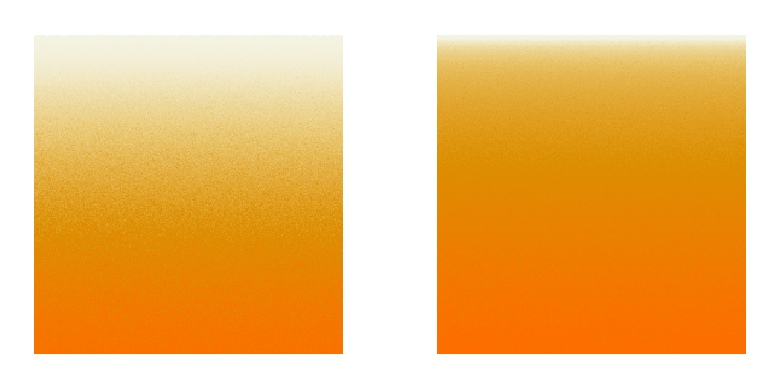

```mathematica
(* here instead we need everything we got till now, the exp fnc, its PDF and its inverted CDF, we ain't going to simulate the exp gradient with a randomwalk however we'll get the sdistance from the stochastic evaluation of the inverse CDF over the unit square *)

ClearAll["Global`*"];
imageSize = Medium;
fncScaling=True;            (* set it to False to have the gradient properly in BW *)
nRndSamples = 64;             (* the higher, the less noise in the gradient, the higher calc time, smooth for >512 *)
freq=256;                             (* because we divide our rnd by this, it will also influence the stochastic outcome *)

expFnc[σ_,s_]=Exp[-(σ*s)];
expPDF[σ_,s_]=σ*Exp[-(σ*s)];
expSample[σ_, rnd_]=-Log[1-rnd]/σ;

f[i_,σ_]:=Module[{s,d,datas},
datas=Table[expSample[σ,RandomReal[]/i],{x,nRndSamples}];
                                               (* draw n 'probable' distances; note: rnd/freq *)
s=Mean[datas];            (* get their average *)
s=s/expPDF[σ,s];     (* divide it by the PDF, aka importance sampling *)
s=s*20;                          (* optional: compress/enlarge exp over the unit *)
d=expFnc[σ,s];          (* feed the exp fnc with the stochastic distance *)
d                                            (* get back with our transmittance at the point *)
]

GraphicsGrid[{
{With[{σ=0.1},                                                                                              (* different sigmas *)
expdata=ParallelTable[f[x,σ],{x,freq},{y,freq}];      
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
],
With[{σ=1},
expdata=ParallelTable[f[x,σ],{x,freq},{y,freq}];     (* note, parallel execution *)
MatrixPlot[expdata,PlotRange->{0,1},ColorFunctionScaling->fncScaling,Frame->False,ImageSize->imageSize]
]}
}]
```

Direction Sampling

[see -> PT SSS Using Anisotropic Phase Functions and Non-Exponential Free Flights]
The relationship between incoming and outgoing directions is represented by a phase function, which assigns a probability to each incoming/outgoing direction pair. Since only the relative angle between the two directions is relevant, phase functions map one-dimensional angle quantity to a one-dimensional probability.

The most popular phase function is Henyey-Greenstein, often abbreviated as HG. The parameter g (generally called the mean cosine) controls the anisotropic bias, with g = 0 being an isotropic distribution, g = 1 being a forward Dirac response and g = −1 being a backward Dirac response. Here ‘Dirac’ means close to a single direction, ie. the lobe is so elongated that looks like a sharp sword... ie. at g=1, μ=1; at g=-1, μ=-1;

P(Θ)=1/(4π)(1-g^2)/((1+g^2-2g Cos[Θ])^(3/2)), such that ∫_0^π P(Θ)2π Sin[Θ]ⅆΘ=1
with g=∫_o^π p(Θ)Cos[Θ]2π Sin[Θ]ⅆΘ

It is common practice to express the Henyey-Greenstein function as the function p(cosΘ)**;
P(μ)=1/(4π)(1-g^2)/((1+g^2-2g μ)^(3/2)), such that ∫_0^π P(μ)Cos[Θ]2π Sin[Θ]ⅆΘ=1
with g=∫_o^π p(μ)Cos[Θ]ⅆμ

** BTW, why Cos[θ] ? Because when we try to find out what component of one vector is in the same direction as another vector, we do something called projection of the first vector onto the second one, that will give us the fraction of the length of a vector pointing in the same direction as the other vector (which is the definition of dot product). To do this, draw a line from the tip of the first vector down onto the second vector. This line should be perpendicular to the second vector. When we have done this, we have literally formed a right-angled triangle whose hypotenuse is the first vector, and whose adjacent side is the projection of that vector onto the second vector. So the ratio of lengths (projection of vector 1 onto vector 2) / (vector 1) is literally given by (adjacent side of right triangle) / (hypotenuse of right triangle), and this ratio is by definition the cosine of the angle. That’s what cosine means. It’s the ratio of the lengths of those two particular sides of the right triangle.


With isotropic we simply mean that a particle scatters photons in every direction with equal probabilities, so its PDF will be 1/2.

```mathematica
normfactor=2π;(1/(4π)*1)*normfactor
```

1/2

Effectively for g=0 the whole second term in the HG equation will be simply 1 reducing HG PDF to that of a sphere of directions. 
When g≠0 then it is anisotropic. 

[see -> https://www.scratchapixel.com/lessons/advanced-rendering/volume-rendering-for-artists]
Now, how does it happen that when a photon collides with an atomic particle the direction it will take is biased toward a certain direction ? Simply put, it does not happen :) 

Effectively when a photon collides with a single particle its chances of taking a certain direction are _always_ uniformly distributed. It is when we have more than one particle in the medium that we may have anisotropy. This happens because of the so called wave interference. In the case of dense homogeneous media  the spacing between particles may be much less than the light wavelength and in that particular case photons traveling through the medium are affected by what is called the phenomenon of wave interference. There may be a constructive or desctructive interference. These interferences depends on the phase shift between the two waves. In mediums made of organised matter, that is, matter where particles are so close to each other that they arrange themselves in organised structures (aka regular patterns), light waves are heavily affected by the wave interference phenomenon while they propagate through these mediums.

However remeber that we said that here we'll deal with linear transport theory, - particles do not interact with each other nor electromagnetic waves collides with each others. Beside the involved theory, the simulation will take ages to converge. That's the cool thing about the HG phase function. It can be used as a mathematical tool to describe anisotropy without having to simulate its underlying physical behaviour. 

The anisotropy or in this case the asymmetry factor g depends (for the same reason above) on the size of the particles. Particles that are small compared to the wavelength of the radiation, such as air molecules, have asymmetry factors close to zero. Larger particles, such as cloud droplets, typically have asymmetry factors ∼0.85 for visible radiation, consistent with strong forward scattering. g is called the mean cosine and is equal to :

g=⟨CosΘ⟩=(∫p(u)cos(u)ⅆu)/(∫p(u)ⅆu)

Why ‘mean’ ? Because it takes into account all the scattering bodies of the medium as a whole ‘mean’ scattering body.

As before, having a probability distribution functions we need a sampling fnc from that to be able to use in a MC env.
Let’s start by seeing if its normalized and from there get it CDF and eventually invert it.

```mathematica
ClearAll["Global`*"]
pHG[u_,g_]=1/(4π)*(1-g^2)/((1+g^2-2g u)^(3/2)); (* u=Cos[θ] where Θ ∈ [0,π]rad*)
Integrate[pHG[u,g],{u,-1,1},Assumptions->g>-1&&g<1] (* let's check it's a PDF.. integrates to 1 *)

(* normalize it so it becomes a PDF *)
𝒟=ProbabilityDistribution[pHG[u,g],{u,-1,1},Assumptions->g>-1&&g<1,Method->"Normalize"]
𝒟/.ProbabilityDistribution->Integrate (* re-check it integrates to 1 *)

(* from PDF find its CDF *)
CDF[𝒟]
(*tmpCDF=Integrate[2 Pi pHG[u,g],{u,-1,u},Assumptions->g>-1&&g<1&&u<1, GenerateConditions->False]*)(* same as above *)

(* eventually invert it to find the direction sampling *)
InverseCDF[𝒟,ξ];
FullSimplify[%]
(*FullSimplify[Solve[tmpCDF==ξ,u]] *)(* same as above *)
```

1/(2 π)

ProbabilityDistribution[(1-g^2)/(2 (1-2 x g+g^2)^(3/2)),{x,-1,1},Assumptions→g>-1&&g<1]

1

Function[x,Piecewise[{{1, x≥1}, {((-1+g) (-1-g+√(1-2 x g+g^2)))/(2 g √(1-2 x g+g^2)), -1<x<1}, {0, True}}],Listable]

ConditionalExpression[Piecewise[{{-1, ξ≤0}, {1, ξ≥1}, {-((-1+g)^2+2 (-1+g) (1+g^2) ξ-2 g (1+g^2) ξ^2)/(1+g (-1+2 ξ))^2, True}}],0≤ξ≤1]

So our HG stuff is :

```mathematica
pdfHG[u_,g_]:=1/2 (1-g^2)/((1+g^2-2 g u)^(3/2));
cdfHG[u_,g_]:= ((-1+g) (-1-g+√(1+g^2-2 g u)))/(2 g √(1+g^2-2 g u));
sampleHG = -((-1+g)^2+2 (-1+g) (1+g^2) ξ-2 g (1+g^2) ξ^2)/(1+g (-1+2 ξ))^2;
samplingHG[g_]:=-((-1+g)^2+2 (-1+g) (1+g^2) #-2 g (1+g^2) #^2)/(1+g (-1+2 #))^2&[RandomReal[]];
```

Now let’s check we got something that works

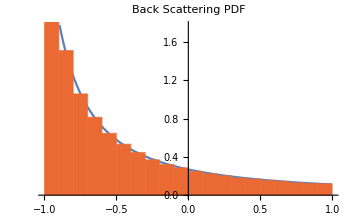

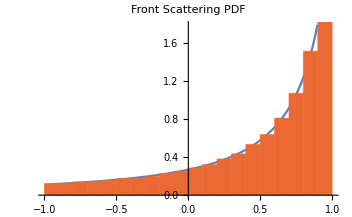

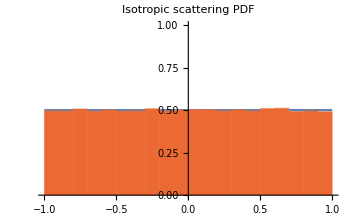

```mathematica
With[{g=-0.5},(* back scattering *)
Show[
Plot[pdfHG[u,g],{u,-1,1},PlotLabel->Style[Framed["Back Scattering PDF"],12,RGBColor[0.5,0.68,0.91]]],
Histogram[ParallelTable[samplingHG[g],{i,Range[10^5]}],Automatic,"PDF",PlotTheme->"WarmColor",PlotRange->All]
]]
With[{g=0.5}, (* front scattering *)
Show[
Plot[pdfHG[u,g],{u,-1,1},PlotLabel->Style[Framed["Front Scattering PDF"],12,RGBColor[0.5,0.68,0.91]]],
Histogram[ParallelTable[samplingHG[g],{i,Range[10^5]}],Automatic,"PDF",PlotTheme->"WarmColor",PlotRange->All]
]]
With[{g=0.0}, (* isotropic *)
Show[
Plot[pdfHG[u,g],{u,-1,1},PlotLabel->Style[Framed["Isotropic scattering PDF"],12,RGBColor[0.5,0.68,0.91]]],
Histogram[ParallelTable[samplingHG[g],{i,Range[10^5]}],Automatic,"PDF",PlotTheme->"WarmColor",PlotRange->All]
]]
```

We see that for back scattering for example we have much more chances to get a cosine of -1 than anything else.
While for isotropic scattering we have a uniform distribution : 1/(b-a)=1/(1-(-1)=1/2=0.5.

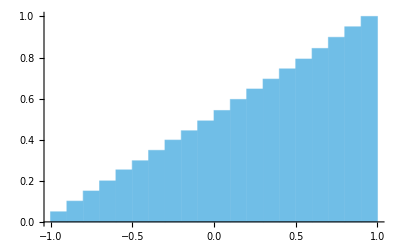

```mathematica
With[{g=0.0}, (* visualize we're accumulating probabilities up to 1 *)
Histogram[ParallelTable[samplingHG[g],{i,Range[10^4]}],Automatic,"CDF",PlotTheme->"PastelColor",PlotRange->All]]
```

Not last, we can also check what PDF we get when explicitly use the cosine for an actual random variate.

```mathematica
Clear[g,ξ];
FullSimplify[pHG[sampleHG,g],Assumptions->(-1<g<1)&&(0<ξ<1)]
```

(1+g (-1+2 ξ))^3/(4 (-1+g^2)^2 π)

We can also check what’s the full range of the PDF over our random variable, that of course will resemble the orange histograms above. We see we have some constant probability around g=0 and that starts increasing more and more while approach g=1;

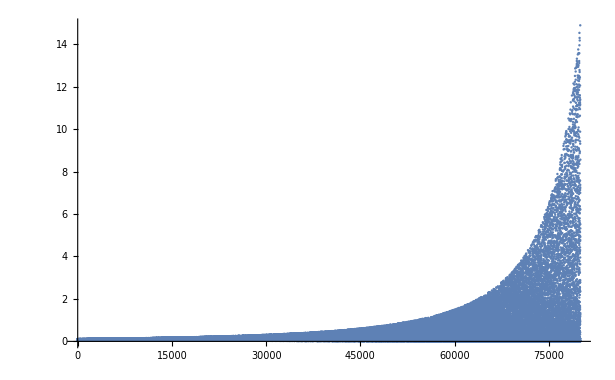

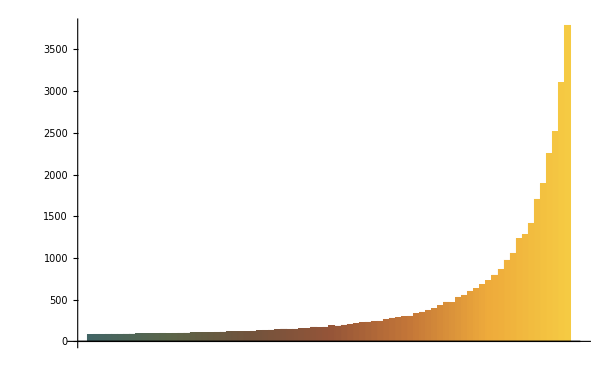

```mathematica
(* subdivide costheta range by .. *)
hgList=Table[pHG[samplingHG[g],g],{g,0.1,0.9,0.00001}];
ListPlot[%,PlotRange->Full]

(* wanna a custom 'histogram' ? *)
plst=Partition[hgList,1000];                              (*divide list*)
slst=Map[Total,plst];                                             (*get each chunck sum*)
BarChart[slst,ChartStyle->"FallColors"]       (*display them as bar charts*)
(* here it's nice to see that the green coloring is for constant prob *)
```

Following will solve this :

∫_o^θ P_hg(θ')ⅆ θ'=ξ

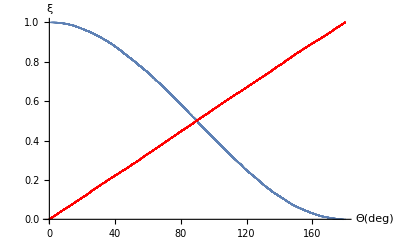

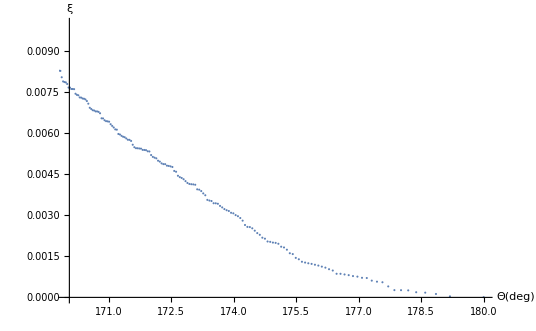

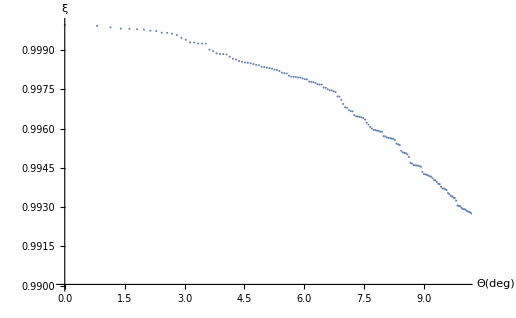

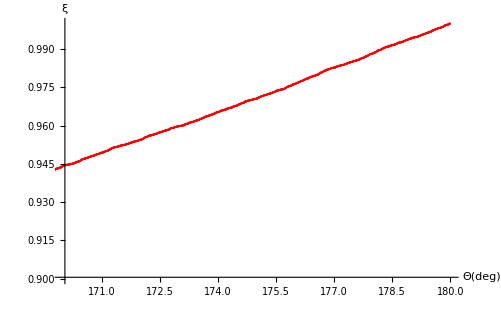

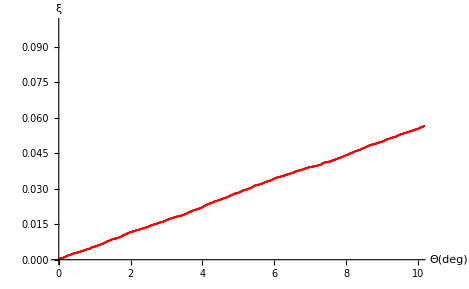

```mathematica
rndTheta[isTheta_:False,g_:0.0,step_:0.001]:=
Module[{ru,rhg,r,ttt,nPts,posHG,pttt,ttx,rndx,xcos,xyttt},
If[isTheta,
ru=Range[0,π,step];                                                             (* quadrature setup*)
rhg=Rescale[pHG[ru,g]];                                                       (* these are probabilities(0-1) corresponding to those ⅆθ*)
,
ru=Range[-1,1,step];
rhg=Rescale[pHG[ru,g]]; 
];

r=Sort[Table[RandomReal[],Length[rhg]]];                     (* let's shot n rnd variates as many interpolation pts *)
ttt=Transpose[{r,ru,rhg}];

nPts=Flatten[Sort[Nearest[rhg,r,1]]];                          (* let's match those variates with their probabilities *)
posHG=Flatten[Position[rhg,Alternatives@@nPts]];(* list of pos that corresponds to pHG*)

pttt=ttt[[posHG]];                                                                       (* find out what entries correspond to those positions *)
ttx = Transpose[pttt];
rndx=ttx[[1]] ;                                                                               (* and so the associated random variates, r *)
xcos=ttx[[2]] ;                                                                               (* with their associated cosines, ru *)

xyttt={};
If[isTheta,
xyttt=Transpose[{xcos*(180/π),rndx}] ;                     (*rearrange so x is theta(deg) and y is rnd*)
,
xyttt=Transpose[{ArcCos[xcos]*(180/π),rndx}];
];
xyttt
]

(* plot ta shit *)
Show[
ListPlot[rndTheta[False,0.0,0.0001],AxesLabel->{"Θ(deg)","ξ"},PlotRange->{{0,180},{0,1}}],
ListPlot[rndTheta[True,0.0,0.0002],PlotStyle->{Red}]
]
ListPlot[rndTheta[False,0.0,0.0001],AxesLabel->{"Θ(deg)","ξ"},PlotRange->{{170,180},{0,0.01}}]
ListPlot[rndTheta[False,0.0,0.0001],AxesLabel->{"Θ(deg)","ξ"},PlotRange->{{0,10},{0.99,1}}]

ListPlot[rndTheta[True,0.0,0.0001],AxesLabel->{"Θ(deg)","ξ"},PlotRange->{{170,180},{0.9,1.0}},PlotStyle->{Red}]
ListPlot[rndTheta[True,0.0,0.0001],AxesLabel->{"Θ(deg)","ξ"},PlotRange->{{0,10},{0.0,0.1}},PlotStyle->{Red}]
```

[see → The Use of the HGF in MC Simulations in Biomedical Optics]
The integral above has been numerically evaluated by using a fix quadrature. This gives a monotonically increasing table of values as a function of θ. The obtained values have been normalized from 0 to 1. Thus, for a randomly generated ξ value it is easy to find the corresponding angle θ by linear interpolation. By construction, θ obtained by generating a set of uniformly distributed values ξ follow the distribution law given by equation (1) and can be utilized for the MC simulation.

It clearly shows how costheta is not evenly distributed for small and big angles while theta is.
Remember that costheta approach belongs to MC context while the theta one is more for wave optics and physics.

```mathematica
(*
(* TODO :: let's try Toublanc (19996) method too where instead of normalizing in 0-1, he's making all add up to 1 *)
phPDFs/Total[phPDFs];
Total[%];
*)
```

TODO :: PolarPlots with PDF vs iCDF !?
TODO :: subdivide costheta - costheta+ⅆt range by .. then see if outcomes are uniformly distributed

```mathematica
(*  *)
hgList=Table[pHG[samplingHG[g],g],{g,0.1,0.9,0.00001}];
```